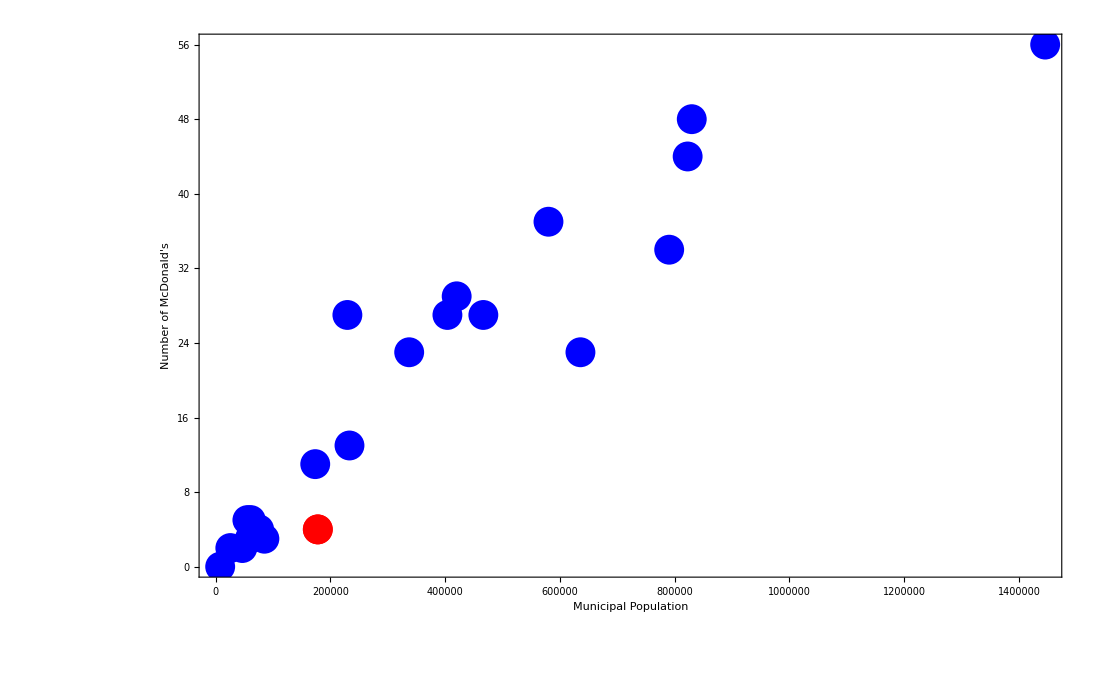

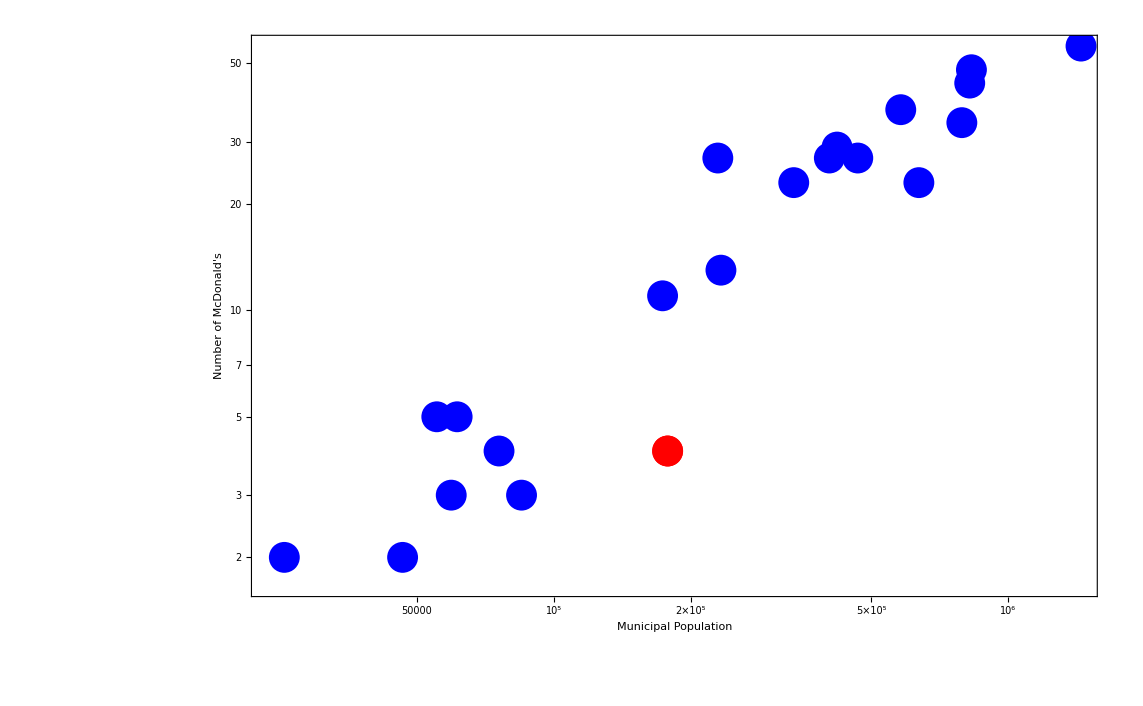

```mathematica
mcdCities = {{59466, 3, "Cheyenne, WY"}, {7855, 0, "Montpelier, VT"}, {337256, 23,"Honolulu, HI"}, {25527, 2, "Frankfort, KY"}, {55274, 5, "Carson City, NV"}, {173514, 11, "Jackson, MS"}, {46478, 2, "Olympia, WA"}, {420003, 29, "Atlanta, GA"}, {61272,5, "Bismarck, ND"}, {466488, 27, "Sacramento, CA"}, {84913, 3, "Trenton, NJ"}, {403892, 27, "Raleigh, NC"},  {635710, 23, "Nashville, TN"},{790390, 34, "Austin, TX"}, {233209, 13, "Madison, WI"}, {822553, 44, "Columbus, OH"}, {580000, 37, "Oklahoma City, OK"}, {1445632, 56, "Phoenix, AZ"}, {75764, 4, "Santa Fe, NM"}, {229553, 27, "Baton Rouge, LA"}, {829718, 48, "Indianapolis, IN"}};
trentonNJ = {{178012,4}};
ListPlot[{trentonNJ,mcdCities[[All,1;;2]]}, Axes->False,Frame->True, FrameLabel->{"Municipal Population","Number of McDonald's"}, PlotStyle->{Red, Blue}, BaseStyle->{FontFamily->"Helvetica Neue",FontSize->16}]
ListLogLogPlot[{trentonNJ,mcdCities[[All,1;;2]]}, Axes->False,Frame->True, FrameLabel->{"Municipal Population","Number of McDonald's"}, PlotStyle->{Red, Blue}, BaseStyle->{FontFamily->"Helvetica Neue",FontSize->16}]
```